```mathematica
Quit[];
```

### Parameter Specification/Summary Stats

```mathematica
MPsubs = {μ-> 1.018, σ ->  0.036, ρ -> -0.14, β-> 0.95};
FSsubs = {μ-> 1.019, σ ->  0.032, ρ -> 0.405, β -> 0.989};
PWsubs = {μ-> 1.019, σ ->  0.020, ρ -> 0.320, β-> 0.988};
```

```mathematica
MPsubsnoρ = {μ-> 1.018, σ ->  0.036, α -> 2, β-> 0.984};
FSsubsnoρ= {μ-> 1.019, σ ->  0.032, α -> 2, β -> 0.989};
PWsubsnoρ = {μ-> 1.019, σ ->  0.020, α -> 2, β-> 0.988};
```

```mathematica
π11 = ϕ/.{ϕ-> (1+ρ)/2}
λ1 = μ+σ
π12  = 1-ϕ/.{ϕ-> (1+ρ)/2};
λ2 = μ-σ;
π21 = π12 ;
π22 = π11;
```

(1+ρ)/2

μ+σ

```mathematica
Eλ1 = π11 λ1 + π12  λ2//FullSimplify
```

μ+ρ σ

```mathematica
Eλ2 = π21 λ1 + π22 λ2//FullSimplify
```

μ-ρ σ

```mathematica
Vλ1 = π11 λ1^2 + π12  λ2^2 - Eλ1^2//FullSimplify
```

-(-1+ρ^2) σ^2

```mathematica
Vλ2 = π21 λ1^2 + π22 λ2^2 - Eλ2^2//FullSimplify;
```

```mathematica
Vλ1 - Vλ2
```

0

### Risk Neutral Probabilities, Risk Premiums, Forward Rates

```mathematica
p11 = (π11  λ1^-α)/(π11  λ1^-α + π12  λ2^-α)//FullSimplify;
```

```mathematica
p12 = (π12  λ2^-α)/(π11  λ1^-α + π12  λ2^-α)//FullSimplify;
```

```mathematica
p21 = (π21  λ1^-α)/(π21  λ1^-α + π22  λ2^-α)//FullSimplify;
```

```mathematica
p22 = (π22  λ2^-α)/(π21  λ1^-α + π22  λ2^-α)//FullSimplify;
```

```mathematica
b11 = β(π11 λ1^-α+π12 λ2^-α)/.{ϕ-> (1+ρ)/2}
b12 = β(π21 λ1^-α+π22 λ2^-α)/.{ϕ-> (1+ρ)/2}
```

β ((1+1/2 (-1-ρ)) (μ-σ)^-α+1/2 (1+ρ) (μ+σ)^-α)

β (1/2 (1+ρ) (μ-σ)^-α+(1+1/2 (-1-ρ)) (μ+σ)^-α)

```mathematica
b21 = b11(p11 b11 + p12 b12)//FullSimplify
```

1/4 β^2 (-(-1+ρ^2) (μ-σ)^(-2 α)+(1+ρ)^2 (μ+σ)^(-2 α)-2 (-1+ρ) (μ-σ)^-α (μ+σ)^-α)

```mathematica
b22 = b12(p21 b11 + p22 b12)//FullSimplify
```

1/4 β^2 ((1+ρ)^2 (μ-σ)^(-2 α)-(-1+ρ^2) (μ+σ)^(-2 α)-2 (-1+ρ) (μ-σ)^-α (μ+σ)^-α)

```mathematica
b11/.MPsubs/.α-> 2
b12/.MPsubs/.α-> 2
b21/.MPsubs/.α-> 2
b22/.MPsubs/.α-> 2
b11/.FSsubs/.α-> 2
b12/.FSsubs/.α-> 2
b21/.FSsubs/.α-> 2
b22/.FSsubs/.α-> 2
```

0.929248

0.911048

0.853282

0.83888

0.93101

0.97956

0.881443

0.946606

```mathematica
b11/.PWsubs/.α-> 2
b12/.PWsubs/.α-> 2
b21/.PWsubs/.α-> 2
b22/.PWsubs/.α-> 2
```

0.940639

0.964561

0.892853

0.922934

```mathematica
Eb11 = π11 b11 + π12 b12//FullSimplify;
```

```mathematica
Eb12 = π21 b11 + π22 b12//FullSimplify;
```

```mathematica
Ehpr1 = Eb11/b21;
```

```mathematica
Ehpr2 = Eb12/b22;
```

```mathematica
Ehpr1/.MPsubs/.α-> 2
Ehpr2/.MPsubs/.α-> 2
Ehpr1/.FSsubs/.α-> 2
Ehpr2/.FSsubs/.α-> 2
Ehpr1/.PWsubs/.α-> 2
Ehpr2/.PWsubs/.α-> 2
```

1.07687

1.0984

1.07262

1.01955

1.06263

1.03629

```mathematica
f1 = b11/b21//FullSimplify;
```

```mathematica
f2 = b12/b22//FullSimplify;
```

```mathematica
rp1 = 1/Sqrt[b21]-1/b11//FullSimplify;
```

```mathematica
rp2 = 1/Sqrt[b22]-1/b12//FullSimplify;
```

```mathematica
f1/.MPsubs/.α-> 2
f2/.MPsubs/.α-> 2
rp1/.MPsubs/.α-> 2
rp2/.MPsubs/.α-> 2
```

1.08903

1.08603

0.00642517

-0.00581911

```mathematica
f1/.FSsubs/.α-> 2
f2/.FSsubs/.α-> 2
rp1/.FSsubs/.α-> 2
rp2/.FSsubs/.α-> 2
```

1.05623

1.03481

-0.00897189

0.00694972

```mathematica
f1/.PWsubs/.α-> 2
f2/.PWsubs/.α-> 2
rp1/.PWsubs/.α-> 2
rp2/.PWsubs/.α-> 2
```

1.05352

1.0451

-0.00480467

0.00417263

```mathematica
rp1MPparam = rp1/.MPsubs;
rp1FSparam =  rp1/.FSsubs;
rp1PWparam = rp1/.PWsubs;
```

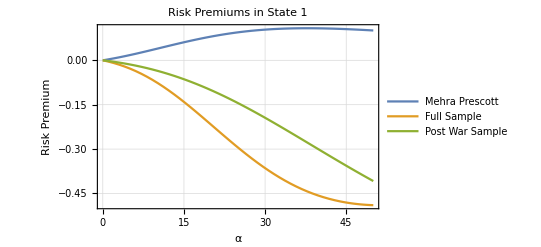

```mathematica
Plot[{rp1MPparam, rp1FSparam, rp1PWparam}, {α, 0, 50}, PlotLegends->{"Mehra Prescott", "Full Sample", "Post War Sample"}, Frame-> True, GridLines->Automatic, AxesLabel->{"α", "Risk Premium"}, PlotLabel->Style["Risk Premiums in State 1",FontSize->18]]
```

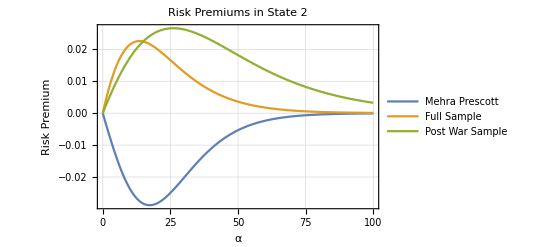

```mathematica
rp2MPparam = rp2/.MPsubs;
rp2FSparam =  rp2/.FSsubs;
rp2PWparam = rp2/.PWsubs;
Plot[{rp2MPparam, rp2FSparam, rp2PWparam}, {α, 0, 100}, PlotLegends->{"Mehra Prescott", "Full Sample", "Post War Sample"}, Frame-> True, GridLines->Automatic, AxesLabel->{"α", "Risk Premium"}, PlotLabel->Style["Risk Premiums in State 2",FontSize->18]]
```

```mathematica
rprhoMP = rp1/.MPsubsnoρ;
rprhoFS = rp1/.FSsubsnoρ;
rprhoPW = rp1/.PWsubsnoρ;
rprhoMP2 = rp2/.MPsubsnoρ;
rprhoFS2 = rp2/.FSsubsnoρ;
rprhoPW2 = rp2/.PWsubsnoρ;
```

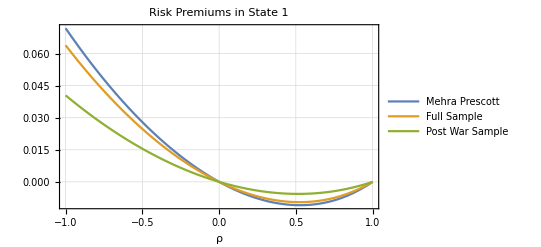

```mathematica
Plot[{rprhoMP, rprhoFS, rprhoPW}, {ρ, -1, 1}, PlotLegends->{"Mehra Prescott", "Full Sample", "Post War Sample"}, Frame-> True, GridLines->Automatic, AxesLabel->Automatic,  PlotLabel->Style["Risk Premiums in State 1",FontSize->18]]
```

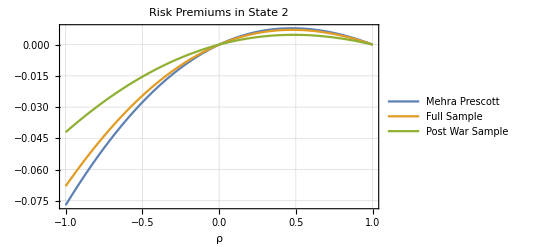

```mathematica
Plot[{rprhoMP2, rprhoFS2, rprhoPW2}, {ρ, -1, 1}, PlotLegends->{"Mehra Prescott", "Full Sample", "Post War Sample"}, Frame-> True, GridLines->Automatic, AxesLabel->Automatic,  PlotLabel->Style["Risk Premiums in State 2",FontSize->18]]
```

### Equity Risk Premium

```mathematica
eq1  = β(π11 λ1^(1-α)(z1 + 1) + π12 λ2^(1-α)(z2+1));
```

```mathematica
eq2 = β(π21 λ1^(1-α)(z1 + 1) + π22 λ2^(1-α)(z2+1));
```

```mathematica
sol = Solve[{eq1-z1==0, eq2-z2==0}, {z1, z2}]//FullSimplify;
```

```mathematica
z1 = (-β (-1+ρ) (μ-σ) (μ+σ)^α+β (μ+σ) ((1+ρ) (μ-σ)^α+2 β ρ (-μ+σ)))/(β (2 β ρ (μ-σ)-(1+ρ) (μ-σ)^α) (μ+σ)+(-β (1+ρ) (μ-σ)+2 (μ-σ)^α) (μ+σ)^α);
```

```mathematica
z2 = (β (1+ρ) (μ-σ) (μ+σ)^α+β (μ+σ) (-(-1+ρ) (μ-σ)^α+2 β ρ (-μ+σ)))/(β (2 β ρ (μ-σ)-(1+ρ) (μ-σ)^α) (μ+σ)+(-β (1+ρ) (μ-σ)+2 (μ-σ)^α) (μ+σ)^α);
```

```mathematica
z1/.MPsubs/.α-> 2
z2/.MPsubs/.α-> 2
z1/.FSsubs/.α-> 2
z2/.FSsubs/.α-> 2
z1/.PWsubs/.α-> 2
z2/.PWsubs/.α-> 2
```

14.268

14.1436

34.1612

35.6236

32.1714

32.7627

```mathematica
Re1 = π11 (λ1(z1 + 1))/z1 +π12 (λ2(z2 +1))/z1//FullSimplify;
```

```mathematica
Re2 = π21 (λ1(z1 + 1))/z2 +π22 (λ2(z2 +1))/z2//FullSimplify;
```

```mathematica
Re1/.MPsubs/.α-> 2
Re2/.MPsubs/.α-> 2
Re1/.FSsubs/.α-> 2
Re2/.FSsubs/.α-> 2
Re1/.PWsubs/.α-> 2
Re2/.PWsubs/.α-> 2
```

1.07907

1.10066

1.07474

1.02145

1.06352

1.03713

```mathematica
Rf1 = 1/b11//FullSimplify;
Rf2 = 1/b12//FullSimplify;
```

```mathematica
Rx1 = Re1 - Rf1//FullSimplify;
```

```mathematica
Rx2 = Re2 - Rf1//FullSimplify;
```

```mathematica
VRx1 =
```

```mathematica
Rx1/.MPsubs/.α-> 2
Rx2/.MPsubs/.α-> 2
Rx1/.FSsubs/.α-> 2
Rx2/.FSsubs/.α-> 2
Rx1/.PWsubs/.α-> 2
Rx2/.PWsubs/.α-> 2
```

0.00293535

0.0245177

0.000635678

-0.0526572

0.000408097

-0.0259759

```mathematica
ERxLR = 1/2 Rx1 + 1/2 Rx2//FullSimplify;
```

```mathematica
VRxLR = 1/2 Rx1^2 + 1/2 Rx2^2 -( 0.5 Rx1 + 0.5 Rx2)^2;
```

```mathematica
ERxLR/.MPsubs/.α-> 2
Sqrt[VRxLR/.MPsubs/.α-> 2]
ERxLR/.FSsubs/.α-> 2
Sqrt[VRxLR/.FSsubs/.α-> 2]
ERxLR/.PWsubs/.α-> 2
Sqrt[VRxLR/.PWsubs/.α-> 2]
```

0.0137265

0.0107912

-0.0260108

0.0266465

-0.0127839

0.013192

```mathematica
ERfLR = 1/2 (Rf1) +1/2 (Rf2);
VRfLR = 1/2 (Rf1)^2 +1/2 (Rf2)^2-(1/2 (Rf1) +1/2 (Rf2))^2//FullSimplify;
```

```mathematica
ERfLR/.MPsubs/.α-> 2
Sqrt[VRfLR/.MPsubs/.α-> 2]
```

1.08689

0.0107487

Calculate Autocorrelations

```mathematica
ρRx1 = (π11(Rx1 - ERxLR) + π12(Rx2 - ERxLR))/(π11 (Rx1 - ERxLR)^2 +π12 (Rx2 - ERxLR)^2-(π11 (Rx1 - ERxLR) +π12 (Rx2 - ERxLR))^2);
ρRx2 = (π21(Rx1 - ERxLR) + π22(Rx2 - ERxLR))/(π21 (Rx1 - ERxLR)^2 +π22 (Rx2 - ERxLR)^2-(π21 (Rx1 - ERxLR) +π22 (Rx2 - ERxLR))^2);
ρRx = 1/2(ρRx1 +ρRx2); 

ρRf1 = (π11(Rf1 - ERfLR) + π12(Rf2 - ERfLR))/(π11 (Rf1 - ERfLR)^2 +π12 (Rf2 - ERfLR)^2-(π11 (Rf1 - ERfLR) +π12 (Rf2 - ERfLR))^2);
ρRf2 = (π21(Rf1 - ERfLR) + π22(Rf2 - ERfLR))/(π21 (Rf1 - ERfLR)^2 +π12 (Rf2 - ERfLR)^2-(π11 (Rf1 - ERfLR) +π12 (Rf2 - ERfLR))^2);
ρRf = 1/2(ρRf1 +ρRf2);
```

```mathematica
ρRx1/.MPsubs/.α-> 2
ρRf1/.MPsubs/.α-> 2
ρRx2/.MPsubs/.α-> 2
ρRf2/.MPsubs/.α-> 2
```

13.233

13.2853

-13.233

-11.6252